# Geometry of Bloch states

## Dirac Systems

```mathematica
(* some general assumptions *)
$Assumptions=Join[Table[k[i]∈Reals,{i,3}],{m∈Reals}];
```

```mathematica
Clear[Η,d,EU,Ε,U,v,vt,nsq]
Η[k_]:=d[k].Table[PauliMatrix[i],{i,3}]
d[k_]:={k[1],k[2],m}
EU[k_]:=Eigensystem[Η[k]]
Ε[k_]=EU[k][[1]];
U[k_]=EU[k][[2]]ᵀ;
(* U is a matrix composed of the eigenvectors, and therefore U† H U = E *)
Inverse[U[k]].Η[k].U[k]-DiagonalMatrix[Ε[k]]//FullSimplify;
(* extract the eigenstates *)
Table[vt[i][k_]=U[k][[;;,i]],{i,Length[U[k]]}];
(* compute the squared norm of the eigenstates *)
Table[nsq[i][k_]=vt[i][k]*.vt[i][k]//FullSimplify,{i,Length[U[k]]}];
(* write the properly normalized states *)
Table[v[i][k_]=vt[i][k]/√(nsq[i][k])//FullSimplify,{i,Length[U[k]]}];
```

```mathematica
(* compute the Berry connection *)
Clear[A]
Table[A[j][k_]=ⅈ Table[(v[j][k]/.{ⅈ->-ⅈ}).D[v[j][k],k[i]]//FullSimplify,{i,3}],{j,Length[U[k]]}]
```

{{-k[2]/(2 (k[1]^2+k[2]^2+m (m+√(m^2+k[1]^2+k[2]^2)))),k[1]/(2 (k[1]^2+k[2]^2+m (m+√(m^2+k[1]^2+k[2]^2)))),0},{-(k[2] (1+m/(√(m^2+k[1]^2+k[2]^2))))/(2 (k[1]^2+k[2]^2)),(k[1] (1+m/(√(m^2+k[1]^2+k[2]^2))))/(2 (k[1]^2+k[2]^2)),0}}

```mathematica
Clear[fv]
fv[kx_,ky_,m_]=A[1][k]/.{k[1]->kx,k[2]->ky,k[3]->0}//FullSimplify;
<<MaTeX`
Manipulate[Show[DensityPlot[Norm[fv[kx,ky,m]],{kx,-1.,1.},{ky,-1.,1.},ColorFunction->"SunsetColors",MaxRecursion->10,PlotPoints->20,PlotLabel->MaTeX["\\text{Berry connection}"],FrameLabel->MaTeX[{"k_x","k_y"}],PlotTheme->"Scientific",PlotLegends->Automatic],StreamPlot[fv[kx,ky,m][[;;2]],{kx,-1.,1.},{ky,-1.,1.},StreamColorFunction->None,StreamStyle->Black,ColorFunction->"SunsetColors",PlotLabel->MaTeX["\\text{Berry curvature}"],FrameLabel->MaTeX[{"k_x","k_y"}],PlotTheme->"Scientific",PlotLegends->Automatic]],{{m,0.2},10^-3,1.}]
```

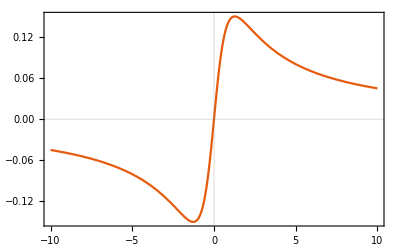

```mathematica
Plot[Evaluate@fv[kx,0,1][[2]],{kx,-10,10},PlotTheme->"Scientific",FrameLabel->MaTeX[{"k_x","A_y"}]]
```

```mathematica
(* compute the Berry curvature *)
Clear[Ω]
Table[Ω[ii][k_]=Table[Sum[Signature[{i,j,l}]D[A[ii][k][[j]],k[l]],{j,3},{l,3}],{i,3}]//FullSimplify,{ii,Length[U[k]]}]
```

{{0,0,-m/(2 (m^2+k[1]^2+k[2]^2)^(3/2))},{0,0,m/(2 (m^2+k[1]^2+k[2]^2)^(3/2))}}

```mathematica
f[kx_,ky_,m_]=Ω[1][k][[3]]/.{k[1]->kx,k[2]->ky};
```

```mathematica
<<MaTeX`
Manipulate[DensityPlot[f[kx,ky,m],{kx,-1.,1.},{ky,-1.,1.},PlotRange->Full,ColorFunction->"SunsetColors",MaxRecursion->10,PlotPoints->20,PlotLabel->MaTeX["\\text{Berry curvature}"],FrameLabel->MaTeX[{"k_x","k_y"}],PlotTheme->"Scientific",PlotLegends->Automatic],{{m,0.2},10^-3,1.}]
```

```mathematica
(* over the Bloch sphere *)
Clear[ϕ,θ,k,s]
$Assumptions=Join[Table[k[i]∈Reals,{i,2}],{m∈Reals,m^2+k[2]^2>=0}];

ϕ[k_]=ArcTan[-d[k][[1]],-d[k][[2]]];
θ[k_]=ArcCos[-d[k][[3]]/Norm[d[k]]];

(* the state which is anti-aligned with d *)
s[1][k_]=MatrixExp[-ⅈ PauliMatrix[3]ϕ[k]/2].MatrixExp[-ⅈ PauliMatrix[2]θ[k]/2].{1,0};

ϕ[k_]=ArcTan[d[k][[1]],d[k][[2]]];
θ[k_]=ArcCos[d[k][[3]]/Norm[d[k]]];

(* the aligned state *)
s[2][k_]=MatrixExp[-ⅈ PauliMatrix[3]ϕ[k]/2].MatrixExp[-ⅈ PauliMatrix[2]θ[k]/2].{1,0};
```

```mathematica
(* these states are Eigenstates of Η and orthogonal by construction *)
s[1][k]†.Η[k].s[1][k]//FullSimplify
s[2][k]†.Η[k].s[2][k]//FullSimplify
s[1][k]†.s[2][k]//FullSimplify
```

-√(m^2+k[1]^2+k[2]^2)

√(m^2+k[1]^2+k[2]^2)

0

```mathematica
(* the two states effectively only differ by a complex phase ⅇ^(-ⅈϕ[k]/2) :) *)
s[1][k]†.v[1][k]//FullSimplify
s[2][k]†.v[2][k]//FullSimplify
```

(ⅇ^(-1/2 ⅈ ArcTan[-k[1],-k[2]]) (√((k[1]^2+k[2]^2) (1-m/(√(m^2+k[1]^2+k[2]^2))))+√((1+m/(√(m^2+k[1]^2+k[2]^2))) (k[1]^2+k[2]^2+2 m (m+√(m^2+k[1]^2+k[2]^2))))))/(2 √(k[1]^2+k[2]^2+m (m+√(m^2+k[1]^2+k[2]^2))))

ⅇ^(-1/2 ⅈ ArcTan[k[1],k[2]])

```mathematica
(* compute the Berry connection from these states *)
Clear[As]
Table[As[j][k_]=ⅈ Table[s[j][k]†.D[s[j][k],k[i]]//FullSimplify,{i,3}],{j,Length[U[k]]}];
```

```mathematica
Clear[fvs]
fvs[kx_,ky_,m_]=(As[1][k])/.{k[1]->kx,k[2]->ky}//FullSimplify;
<<MaTeX`
Manipulate[Show[DensityPlot[Norm[fvs[kx,ky,m]],{kx,-1.,1.},{ky,-1.,1.},ColorFunction->"SunsetColors",MaxRecursion->10,PlotPoints->20,PlotLabel->MaTeX["\\text{Berry connection}"],FrameLabel->MaTeX[{"k_x","k_y"}],PlotTheme->"Scientific",PlotLegends->Automatic],StreamPlot[fvs[kx,ky,m][[;;2]],{kx,-1.,1.},{ky,-1.,1.},StreamColorFunction->None,StreamStyle->Black,ColorFunction->"SunsetColors",PlotLabel->MaTeX["\\text{Berry curvature}"],FrameLabel->MaTeX[{"k_x","k_y"}],PlotTheme->"Scientific",PlotLegends->Automatic]],{{m,0.2},10^-3,1.}]
```

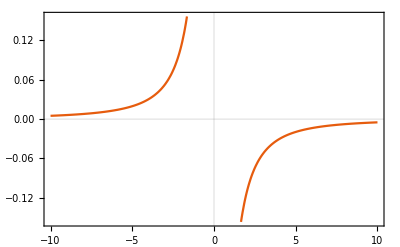

```mathematica
Plot[Evaluate@fvs[kx,0,1][[2]],{kx,-10,10},PlotTheme->"Scientific",FrameLabel->MaTeX[{"k_x","A_y"}]]
```

```mathematica
(* the connection is different in this basis! *)
Table[A[i][k]-As[i][k],{i,2}]//FullSimplify
```

{{-k[2]/(2 (k[1]^2+k[2]^2)),k[1]/(2 (k[1]^2+k[2]^2)),0},{-k[2]/(2 (k[1]^2+k[2]^2)),k[1]/(2 (k[1]^2+k[2]^2)),0}}

```mathematica
(* the difference between the two is exactly the gradient of the phase difference between the states *)
1/2 Grad[ArcTan[k[1],k[2]],{k[1],k[2],k[3]}]
```

{-k[2]/(2 (k[1]^2+k[2]^2)),k[1]/(2 (k[1]^2+k[2]^2)),0}

```mathematica
(* compute the Berry curvature *)
Table[Ωs[ii][k_]=Table[Sum[Signature[{i,j,l}]D[As[ii][k][[j]],k[l]],{j,3},{l,3}],{i,3}]//FullSimplify,{ii,Length[U[k]]}]
```

{{0,0,-m/(2 (m^2+k[1]^2+k[2]^2)^(3/2))},{0,0,m/(2 (m^2+k[1]^2+k[2]^2)^(3/2))}}

```mathematica
(* the curvature is the same! *)
Table[Ω[i][k]-Ωs[i][k],{i,2}]
```

{{0,0,0},{0,0,0}}

```mathematica
(* when we integrate the curvature over the sphere, we get the total flux *)
Integrate[-m/(2π (m^2+kx^2+ky^2)^(3/2)),{kx,-∞,∞},{ky,-∞,∞}]
```

-Sign[m]